```mathematica
α={0.6, 0.7, 0.8, 1.1}; n=100;
```

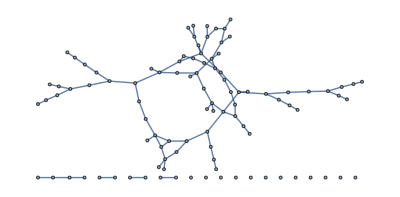

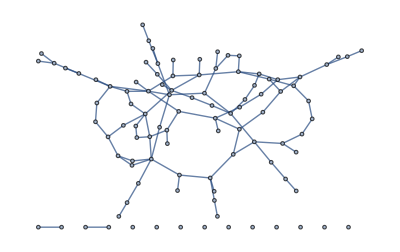

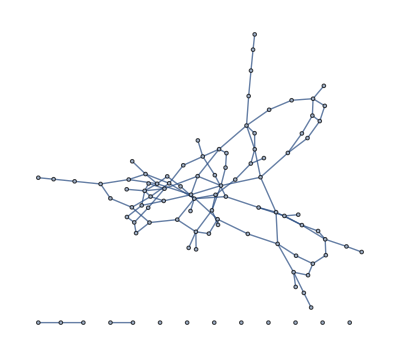

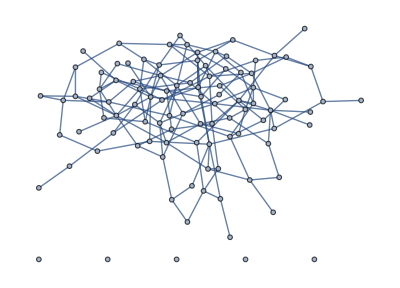

```mathematica
For[i=1, i≤Length[α], i++, {r=RandomGraph[{n, Round[3.*α[[i]]*n/2]}], Print[Graph[r]]}]
```